```mathematica
.00
```

```mathematica
EDO01=x''[t]+0.4x'[t]+9.04x[t]== 6 Exp[-t/5]Cos[3 t]
paso1=LaplaceTransform[EDO01,t,s]
paso2=paso1/.{x[0]->0,x'[0]->0}
paso3=Solve[paso2,LaplaceTransform[x[t],t,s]]
```

9.04 x[t]+0.4 x'[t]+x''[t]==6 ⅇ^(-t/5) Cos[3 t]

9.04 LaplaceTransform[x[t],t,s]+s^2 LaplaceTransform[x[t],t,s]+0.4 (s LaplaceTransform[x[t],t,s]-x[0])-s x[0]-x'[0]==(6 (1/5+s))/(9+(1/5+s)^2)

9.04 LaplaceTransform[x[t],t,s]+0.4 s LaplaceTransform[x[t],t,s]+s^2 LaplaceTransform[x[t],t,s]==(6 (1/5+s))/(9+(1/5+s)^2)

{{LaplaceTransform[x[t],t,s]→(6. (0.2+s))/((9.04+0.4 s+s^2) (9.+(0.2+s)^2))}}

(0.+0.5 ⅈ) ⅇ^((-0.2-3. ⅈ) t) t-(0.+0.5 ⅈ) ⅇ^((-0.2+3. ⅈ) t) t

ⅇ^(-t/5) t

ⅇ^(-t/5)-1/5 ⅇ^(-t/5) t

-2/5 ⅇ^(-t/5)+1/25 ⅇ^(-t/5) t

-1/(5 ⅇ)

{{t→5}}

{5/ⅇ,{t→5}}

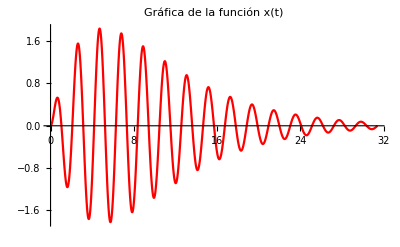

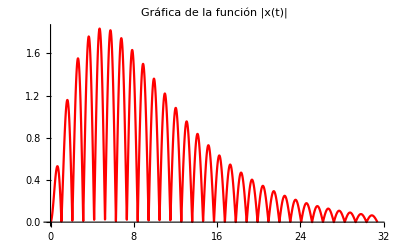

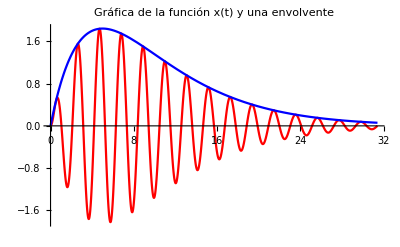

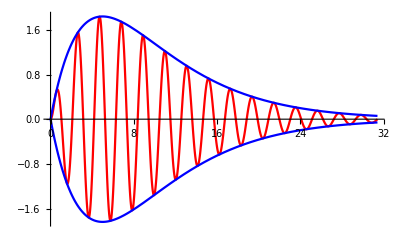

```mathematica
sol=Simplify[InverseLaplaceTransform[(6 (0.2+s))/((9.04+0.4s+s^2)(9+(0.2+s)^2)),s,t]]//Expand
curva=t* Exp[-t/5]
derivada=D[curva,t]
derivada2 = D[curva,{t,2}]
derivada2/.t->5
Solve[derivada==0,t]
Maximize[{curva,(t≥0)&&(t≤30)},t]
Plot[sol,{t,0,10 Pi},PlotLabel->"Gráfica de la función x(t)", LabelStyle->Directive[FontSize->12],PlotStyle->{Red}]
Plot[Abs[sol],{t,0,10 Pi},PlotLabel->"Gráfica de la función |x(t)|", LabelStyle->Directive[FontSize->12],PlotStyle->{Red}]
Plot[{sol, curva},{t,0,10 Pi},PlotLabel->"Gráfica de la función x(t) y una envolvente", LabelStyle->Directive[FontSize->12],PlotStyle->{Red, Blue}]

Plot[{sol,curva, -curva},{t,0,10 Pi},PlotStyle->{{Red,Dashing[None]},{Blue,Dashing[None]}, {Blue,Dashing[None]}}]
```